Wolfram Online Mini Campus. Part 14

Instagram Posts
Pinterest Posts
"Translation" of  SageMath Online Mini Campus. Part 14

Explorations of Color Schemes

```mathematica
SphericalPlot3D[Sin[12θ]*Tan[ϕ/5]+Cos[21ϕ],{θ,0,2 Pi},{ϕ,0,2 Pi},
                                     PlotRange->{{-4,4},{-4,4},{-4,4}},PlotPoints->30,ImageSize->Large,
                Mesh->False,Boxed->False,Axes->False,Exclusions->{Cos[ϕ]==0},
              ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["BrightBands"][.7-r]]]
```

-Graphics3D-

```mathematica
Manipulate[Show[Graphics3D[{Hue[(x+y+z)/9],EdgeForm[Gray],Opacity[.5],Dodecahedron[{x,y,z},1],
                                                         Black,Opacity[1],Style[Text[{x,y,z},{x,y,z}],Italic,11]}],
                    PlotRange->{{-5,5},{-5,5},{-5,5}},Axes->True,AxesStyle->LightGray,BoxStyle->LightGray],
         {x,Range[-3,3,1]},{y,Range[-3,3,1]},{z,Range[-3,3,1]}]
```

```mathematica
L1=Table[{j*Sin[Pi*i/100]+Sin[Pi*i/50],-j*(1+Cos[Pi*i/100]+Cos[Pi*i/50])},{j,20 },{i,Range[-100,101,4]}];
L2=Table[{50+j*Sin[Pi*i/100]+Sin[Pi*i/50],-j*(1+Cos[Pi*i/100]+Cos[Pi*i/50])},{i,Range[-100,101,4]},{j ,20}];
Show[ListLinePlot[L1,PlotStyle->"AvocadoColors"],ListLinePlot[L2,PlotStyle->"FruitPunchColors"],
         ImageSize->{600,400},Axes->False,PlotRange->All,Frame->True]
```

-Graphics-

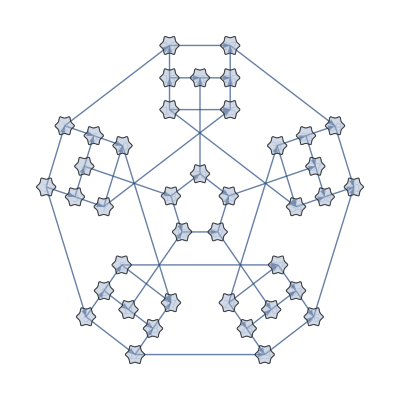
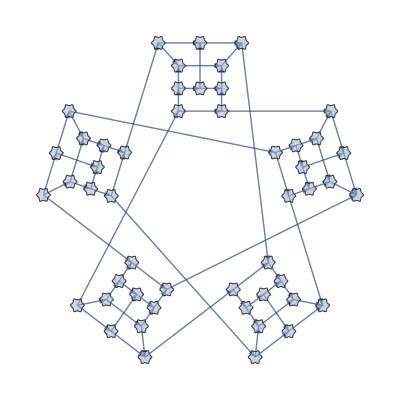

```mathematica
CET=Function[{g,s},Flatten[Table[Table[i<->j->ColorData[s][i/Length[GraphData[g,"Vertices"]]],
                                                          {j,AdjacencyList[GraphData[g],i]}],{i,GraphData[g,"Vertices"]}]]];
CGP= Function[{g,s},GraphPlot[GraphData[g],ImageSize->{400,400},
      VertexLabels->Placed[Automatic,{.5,.4}],VertexSize->.6,EdgeStyle->CET[g,s],
   EdgeShapeFunction->GraphElementData[{"CarvedArcArrow", "ArrowSize"->.03,Opacity->.8}],
      VertexStyle->{RGBColor["Silver"],Opacity[0.5]},VertexShapeFunction->"ConcaveHexagon"]];
{CGP["GoldbergSnark5","DarkRainbow"],CGP["WatkinsSnark","Rainbow"]}
```

Explorations of Tensors

```mathematica
A=ArrayReshape[Array[#1^2 &,8],{2,2,2}]; B=ArrayReshape[{"♔","♕","♖","♗"},{2,2}];
{MatrixForm[A],MatrixForm[B]}
{MatrixForm[Dot[A,B]],MatrixForm[Dot[B,A]],MatrixForm[A*B]}
```

{((1
4) | (9
16)
(25
36) | (49
64)),(♔ | ♕
♖ | ♗)}

{((♔+4 ♖
4 ♗+♕) | (9 ♔+16 ♖
16 ♗+9 ♕)
(25 ♔+36 ♖
36 ♗+25 ♕) | (49 ♔+64 ♖
64 ♗+49 ♕)),((♔+25 ♕
4 ♔+36 ♕) | (9 ♔+49 ♕
16 ♔+64 ♕)
(25 ♗+♖
36 ♗+4 ♖) | (49 ♗+9 ♖
64 ♗+16 ♖)),((♔
4 ♔) | (9 ♕
16 ♕)
(25 ♖
36 ♖) | (49 ♗
64 ♗))}

Explorations of Integrals

```mathematica
F={Log[2+3x^2],x^(1/3)*Log[x],Sqrt[x]*ArcTan[Sqrt[x]],Exp[x]*Sin[2x],Exp[-x]*(x+2),
      4^(-x)*(x+3),x*Log[x]^2,ArcTan[Sqrt[4x-1]],(4x+1)*Cos[2x],(x+5)*Sin[3x]};
Do[Print[TraditionalForm[F[[i]]]->TraditionalForm[Integrate[F[[i]],x]]],{i,10}]
```

log(3 x^2+2)→x log(3 x^2+2)-2 x+2 √(2/3) tan^-1(√(3/2) x)

x^(1/3) log(x)→3/16 x^(4/3) (4 log(x)-3)

√x tan^-1(√x)→1/3 (2 x^(3/2) tan^-1(√x)-x+log(x+1))

ⅇ^x sin(2 x)→1/5 ⅇ^x (sin(2 x)-2 cos(2 x))

ⅇ^-x (x+2)→ⅇ^-x (-x-3)

4^-x (x+3)→-(4^-x (x log(4)+1+log(64)))/(log^2(4))

x log^2(x)→x^2/4+1/2 x^2 log^2(x)-1/2 x^2 log(x)

tan^-1(√(4 x-1))→x tan^-1(√(4 x-1))-1/4 √(4 x-1)

(4 x+1) cos(2 x)→2 x sin(2 x)+1/2 sin(2 x)+cos(2 x)

(x+5) sin(3 x)→1/9 sin(3 x)-1/3 x cos(3 x)-5/3 cos(3 x)

```mathematica
Table[Plot[{F[[i]],Evaluate[Integrate[F[[i]],x]]},{x,0,1}],{i,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Explorations of HTML Objects

```mathematica
EmbeddedHTML["<div id='test'></div>
<script type='module'>
import {Runtime,Inspector,Library} from 'https://unpkg.com/@observablehq/notebook-runtime?module';
import notebook from 'https://api.observablehq.com/d/f523a66288d9ab04.js?key=e76719d4648ff9ff';
const test=document.querySelector('#test');
const main={id:'main',modules:[{id:'main',variables:notebook.modules[0].variables.map(v=>{
      return v.name==='subject' ? Object.assign(v,{value:':d83d:de4b'}):v;})}]};
Runtime.load(main,cell => {if (cell.name==='greeting') {return new Inspector(test);}});
</script>",ImageSize->{200,50}]
```

Null«554»<div id='test'></div>
<script type='module'>
import {Runtime,Inspector,Library} from 'https://unpkg.com/@observablehq/notebook-runtime?module';
import notebook from 'https://api.observablehq.com/d/f523a66288d9ab04.js?key=e76719d4648ff9ff';
const test=document.querySelector('#test');
const main={id:'main',modules:[{id:'main',variables:notebook.modules[0].variables.map(v=>{
      return v.name==='subject' ? Object.assign(v,{value:':d83d:de4b'}):v;})}]};
Runtime.load(main,cell => {if (cell.name==='greeting') {return new Inspector(test);}});
</script>